# MA255 Tech Lab Assignment #3

## I. Double Integrals over General Regions

First, we define the function:

```mathematica
f[x_,y_]=7*x^3+5*y^4;
```

#### a. Compute the volume under the surface over the rectangle bounded by (0,0), (7,0), (7,5), (0,5).

```mathematica
∫_0^5 ∫_0^7 f[x,y]ⅆxⅆy
```

171535/4

#### b. Compute the volume under the surface over the triangle with vertices (0,0), (1,1), (0,1)

```mathematica
∫_0^1 ∫_x^1 f[x,y]ⅆyⅆx
```

71/60

#### c. Compute the volume under the surface over the region bounded by y=x^2-1 and y = -(x-1)^2,0 ≤ x ≤ 1

```mathematica
∫_0^1 ∫_(x^2-1)^(-(x-1)^2) f[x,y]ⅆyⅆx
```

2582/3465

#### d. Compute the volume under the surface over the region bounded by y = -sin x and y = sin x, 0 ≤ x ≤ π

```mathematica
∫_0^Pi ∫_(-Sin[x])^Sin[x] f[x,y]ⅆyⅆx//N
```

172.327

#### e. Compute the volume under the surface over the disk of radius 4 centered at the origin using cartesian coordinates.

```mathematica
∫_-4^4 ∫_(-(16-x^2)^(1/2))^((16-x^2)^(1/2)) f[x,y]ⅆyⅆx
```

2560 π

#### f. Compute the volume under the surface over the disk of radius 4 centered at the origin using polar coordinates.

```mathematica
∫_0^(2*Pi) ∫_0^4 (7*(r*Cos[θ])^3+ 5*(r*Sin[θ])^4)*r ⅆr ⅆθ
```

2560 π

## II. Plotting Regions

#### 1) Plot the region described in (1a)

-Graphics3D-

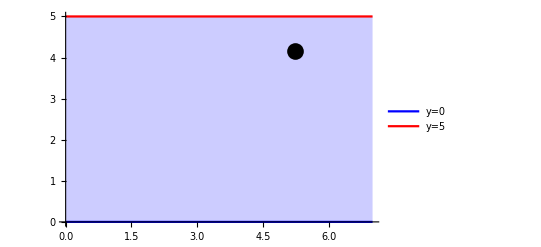

```mathematica
y1[x_]=0;
y2[x_]=5;
p1=Plot[{y1[x],y2[x]},{x,0,7},PlotStyle->{{Blue,Thick},{Red,Thick}},Filling->{1->{2}},PlotLegends->{"y=0","y=5"}];
p2=Plot3D[f[x,y],{x,0,1},{y,0,5},Filling->Bottom,FillingStyle->{Pink,Opacity[0.3]}]
p3=Graphics[{PointSize[0.03],Point[{2233/426,3545/852}]}];
Show[{p1,p3}]
```

The first graph shows the surface plotted over the region while the second graph is a 2D interpretation of the bounds of the graph with the location of the center of mass.

#### 2) Plot the region described in (1b)

-Graphics3D-

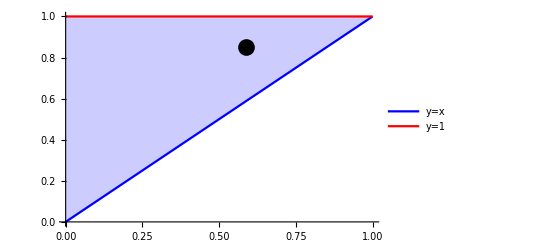

```mathematica
y1[x_]=x;
y2[x_]=1;
p4=Plot[{y1[x],y2[x]},{x,0,1},PlotStyle->{{Blue,Thick},{Red,Thick}},Filling->{1->{2}},PlotLegends->{"y=x","y=1"}];
Plot3D[f[x,y],{x,0,1},{y,y1[x],y2[x]},Filling->Bottom,FillingStyle->{Pink,Opacity[0.3]}]
p5=Graphics[{PointSize[0.03],Point[{10/17,130/153}]}];
Show[{p4,p5}]
```

The first graph shows the surface plotted over the region while the second graph is a 2D interpretation of the bounds of the graph with the location of the center of mass.

#### 3) Plot the region described in (1c)

-Graphics3D-

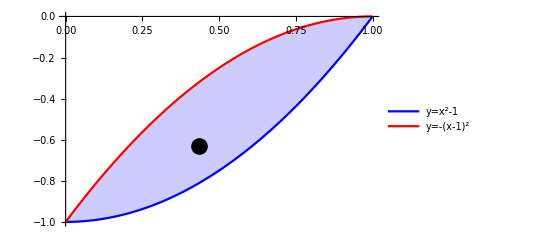

```mathematica
y1[x_]=x^2-1;
y2[x_]=-(x-1)^2;
p6=Plot[{y1[x],y2[x]},{x,0,1},PlotStyle->{{Blue,Thick},{Red,Thick}},Filling->{1->{2}},PlotLegends->{"y=x^2-1","y=-(x-1)^2"}];
Plot3D[f[x,y],{x,0,1},{y,y1[x],y2[x]},Filling->Bottom,FillingStyle->{Pink,Opacity[0.3]}]
p7=Graphics[{PointSize[0.03],Point[{9697/22251,-13994/22251}]}];
Show[{p6,p7}]
```

The first graph shows the surface plotted over the region while the second graph is a 2D interpretation of the bounds of the graph with the location of the center of mass.

## III. Mass and Center of Mass

We assume that there exists a density function such that p(x,y)=xy^2+x^2 y^4 that represents a surface mass density of a lamina.

#### a. Calculate the Total Mass and Center of Mass coordinates of the laminas bounded by (1a), (1b), and (1c). (1a)

```mathematica
p[x_,y_]=x*y^2+x^2*y^4;
xmin=0;
xmax=7;
ymin=0;
ymax=5;
My=∫_xmin^xmax ∫_ymin^ymax x*p[x,y]ⅆyⅆx;
Mx=∫_xmin^xmax ∫_ymin^ymax y*p[x,y]ⅆyⅆx;
m=∫_xmin^xmax ∫_ymin^ymax p[x,y]ⅆyⅆx
{My/m,Mx/m}
```

434875/6

{2233/426,3545/852}

So the center of mass is located at {2233/426,3545/852} .

#### (1b)

```mathematica
p[x_,y_]=x*y^2+x^2*y^4;
xmin=0;
xmax=1;
ymin=x;
ymax=1;
My=∫_xmin^xmax ∫_ymin^ymax x*p[x,y]ⅆyⅆx;
Mx=∫_xmin^xmax ∫_ymin^ymax y*p[x,y]ⅆyⅆx;
m=∫_xmin^xmax ∫_ymin^ymax p[x,y]ⅆyⅆx
{My/m,Mx/m}
```

17/120

{10/17,130/153}

So the center of mass is located at {10/17,130/153}.

#### (1c)

```mathematica
p[x_,y_]=x*y^2+x^2*y^4;
xmin=0;
xmax=1;
ymin=x^2-1;
ymax=-(x-1)^2;
My=∫_xmin^xmax ∫_ymin^ymax x*p[x,y]ⅆyⅆx;
Mx=∫_xmin^xmax ∫_ymin^ymax y*p[x,y]ⅆyⅆx;
m=∫_xmin^xmax ∫_ymin^ymax p[x,y]ⅆyⅆx
{My/m,Mx/m}
```

7417/180180

{9697/22251,-13994/22251}

So the center of mass is located at {9697/22251,-13994/22251} .

## IV. Triple Integrals using Cylindrical Coordinates

A NFL football is bounded by the parabaloids: f(x,y) = -1/2√(121-(πx)^2-(πy)^2) and g(x,y) = 1/2√(121-(πx)^2-(πy)^2). It is 11 inches in length and 22 inches in circumference.

#### a. Find the volume bounded by the football using Cartesian coordinates.

```mathematica
f2[x_,y_]=-.5*(121-(Pi*x)^2-(Pi*y)^2)^(1/2);
g2[x_,y_]=.5*(121-(Pi*x)^2-(Pi*y)^2)^(1/2);
∫_-3.5^3.5 ∫_(-(3.5-x^2)^(1/2))^((3.5-x^2)^(1/2)) ∫_f2[x,y]^g2[x,y] 1ⅆzⅆyⅆx//N
```

#### b. Find the volume bounded by the football using Cylindrical coordinates.

```mathematica
f2[r_,θ_]=-.5*(121-(Pi*r)^2)^(1/2);
g2[r_,θ_]=.5*(121-(Pi*r)^2)^(1/2);
∫_0^(2*Pi) ∫_0^3.5 ∫_f2[r,θ]^g2[r,θ] rⅆzⅆrⅆθ//N
```

282.441

#### c. Consider the mass density function. Find the total mass of the football.

```mathematica
p2[r_,θ_,z_]=5.5*z+3*r^2+11;
θmin=0;
θmax=2*Pi;
rmin=0;
rmax=3.5;
zmin=f2[r,θ];
zmax=g2[r,θ];
m=∫_θmin^θmax ∫_rmin^rmax ∫_zmin^zmax p2[r,θ,z]*rⅆzⅆrⅆθ
```

7261.92

#### d. Using the mass found in (4c), find the coordinates of the center of mass for the football.

```mathematica
p2[r_,θ_,z_]=5.5*z+3*r^2+11;
θmin=0;
θmax=2*Pi;
rmin=0;
rmax=3.5;
zmin=f2[r,θ];
zmax=g2[r,θ];

Myz=∫_θmin^θmax ∫_rmin^rmax ∫_zmin^zmax r*Cos[θ]*p2[r,θ,z]*rⅆzⅆrⅆθ;
Mxz=∫_θmin^θmax ∫_rmin^rmax ∫_zmin^zmax r*Sin[θ]*p2[r,θ,z]*rⅆzⅆrⅆθ;
Mxy=∫_θmin^θmax ∫_rmin^rmax ∫_zmin^zmax z*p2[r,θ,z]*rⅆzⅆrⅆθ;
{Myz/m,Mxz/m,Mxy/m}
```

{0.,0.,1.29421}

## V. Probability

We will explore the joint-density problem of the inflation of an official NFL football. The value x will represent the actual air pressure in the Patriot’s football and the value y will represent the actual air pressure in the Colt’s football.
f (x,y) = {K(x^2+y^2), if 10≤x≤16 and 10≤y≤16;
	 {0,               otherwise

#### a. What value of K makes this a “valid” Probability Density Function?

```mathematica
f[x_,y_]=K*(x^2+y^2)
∫_10^16 ∫_10^16 f[x,y]ⅆxⅆy
```

K (x^2+y^2)

12384 K

```mathematica
Solve[12384 K==1,K]
```

```mathematica
{{K->1/12384}}
```

Thus, the K value that makes this a valid PDF is 1/12384because this is the value where ∫_(-∞)^∞ f(x)ⅆx = 1.

#### b.What is the probability that both balls are underflated?

As stated in the problem, we will use 13 psi as the ideal inflation so anything under 13 psi is underflated.

```mathematica
∫_10^13 ∫_10^13 f[x,y]ⅆxⅆy
2394*(1/12384)
```

2394 K

133/688

Therefore, the probability that both balls are underflated is 133/688.

#### c. What is the probability that both balls are over inflated?

As stated before, 13 psi is the ideal inflation so anything over 13 psi will be considered over inflated.

```mathematica
∫_13^16 ∫_13^16 f[x,y]ⅆxⅆy
3798*(1/12384)
```

3798 K

211/688

Therefore, the probability that both balls are over inflated is 211/688.

#### d. What is the probability that the Patriot’s ball is under inflated and the Colt’s ball is over inflated?

```mathematica
∫_13^16 ∫_10^13 f[x,y]ⅆxⅆy
3096*(1/12384)
```

3096 K

1/4

Therefore, the probability that the Patriot’s ball is under inflated and the Colt’s ball is over inflated is 1/4.